# CCBH: Low BH Mass Detection Consequences

## All the results here are for the direct method

Davi  C. Rodrigues (this code). Sep, 2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled black hole (general case)
DEBH = Dark energy coupled Black Hole (implies k = - 3w)
GBH = Growing BH, k is arbitrary and without direct dark energy impact.
m1 = primary (larger) mass of the BBH or NSBH pair.


Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{"codes", "Directories.wl"}]];

(*
  Calling wl files
  ***************** 
*)
getCode["Constants.wl"];
baseSimPoints = 10^6; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["ObsDataPreparationGWTC-3.wl"]; 
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
Options[plpp`plpp] = {  (*PLPP method is not used here, but I will left here this setting.*)
  plpp`a -> 3.549,
  plpp`mMin -> 0.76, (*This is the single change. Value from Morras et al 2023*)
  plpp`dm -> 5.454,
  plpp`mMax -> 83.140,
  plpp`mu -> 34.467,
  plpp`s -> 1.867,
  plpp`l -> 0.019,
  plpp`betaQ -> 0.760
};
optionsPlpp = Options[plpp`plpp];
getCode["MassFactorCorrection.wl"];

Print[Style["End of running wl files.", FontColor->LightGray]];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

sigmaProb::usage = "sigmaProb[probability] yields the number of σ's for a given probability.";
sigmaProb[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[probSigma];
probSigma[n_] := probSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   1000000

"dataM1Merger"  14.3778

End of running wl files.

## Direct Method

This is an old and quick numerical cross-check. For further details and developments, see Luca Amendola’s GitHub.

```mathematica
mXzDataCentralValues2 = mXzDataForPlotting2 /. Around[x_, y_] -> x;

mXzDataCentralValues2Clean = mXzDataCentralValues2 // SortBy[#, Last] & // Drop[#, 2] & 

mXzDataCentralValues2Morras = mXzDataCentralValues2 // SortBy[#, Last] & // Drop[#, 2] & // Prepend[#, {0.028, 0.76}]&  (*Added event from Morras et al PDU 2023*)
```

{{0.05,2.6},{0.11,5.1},{0.2,6.3},{0.16,6.7},{0.16,6.9},{0.09,7.3},{0.16,7.5},{0.07,7.6},{0.07,7.7},{0.09,7.7},{0.23,7.7},{0.22,7.8},{0.17,7.9},{0.2,7.9},{0.18,8.},{0.13,8.2},{0.15,9.},{0.29,10.4},{0.19,11.6},{0.28,12.5},{0.21,13.6},{0.22,14.},{0.19,15.5},{0.35,18.1},{0.4,18.3},{0.29,18.5},{0.61,19.9},{0.2,20.},{0.28,20.},{0.44,22.2},{0.2,23.8},{0.18,24.},{0.33,24.},{0.57,24.},{0.56,24.2},{0.32,24.5},{0.12,25.2},{0.38,25.8},{0.21,26.7},{0.53,26.8},{0.57,27.1},{0.4,27.4},{0.54,27.6},{0.23,27.7},{0.57,27.9},{0.24,28.3},{0.29,28.3},{0.18,28.9},{0.35,29.},{0.56,29.},{0.63,30.},{0.52,30.2},{0.62,30.4},{0.09,30.6},{0.92,30.6},{0.45,32.},{0.32,32.5},{0.56,32.6},{0.21,33.4},{0.49,34.},{0.29,34.2},{0.51,34.7},{0.5,35.},{0.69,37.},{0.6,39.4},{0.38,40.5},{0.45,40.8},{0.49,44.8},{0.25,47.},{0.56,57.2}}

{{0.028,0.76},{0.05,2.6},{0.11,5.1},{0.2,6.3},{0.16,6.7},{0.16,6.9},{0.09,7.3},{0.16,7.5},{0.07,7.6},{0.07,7.7},{0.09,7.7},{0.23,7.7},{0.22,7.8},{0.17,7.9},{0.2,7.9},{0.18,8.},{0.13,8.2},{0.15,9.},{0.29,10.4},{0.19,11.6},{0.28,12.5},{0.21,13.6},{0.22,14.},{0.19,15.5},{0.35,18.1},{0.4,18.3},{0.29,18.5},{0.61,19.9},{0.2,20.},{0.28,20.},{0.44,22.2},{0.2,23.8},{0.18,24.},{0.33,24.},{0.57,24.},{0.56,24.2},{0.32,24.5},{0.12,25.2},{0.38,25.8},{0.21,26.7},{0.53,26.8},{0.57,27.1},{0.4,27.4},{0.54,27.6},{0.23,27.7},{0.57,27.9},{0.24,28.3},{0.29,28.3},{0.18,28.9},{0.35,29.},{0.56,29.},{0.63,30.},{0.52,30.2},{0.62,30.4},{0.09,30.6},{0.92,30.6},{0.45,32.},{0.32,32.5},{0.56,32.6},{0.21,33.4},{0.49,34.},{0.29,34.2},{0.51,34.7},{0.5,35.},{0.69,37.},{0.6,39.4},{0.38,40.5},{0.45,40.8},{0.49,44.8},{0.25,47.},{0.56,57.2}}

```mathematica
dataM2ObsFormationClean =  #2 /dataMassFactor[#1, tdmin0, tdmax0, k0, zMax0, w0] &  @@@ mXzDataCentralValues2Clean;
dataM2ObsFormationMorras =  #2 /dataMassFactor[#1, tdmin0, tdmax0, k0, zMax0, w0] &  @@@ mXzDataCentralValues2Morras;
```

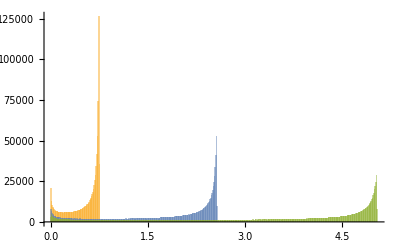

```mathematica
Histogram[{dataM2ObsFormationMorras[[1]], dataM2ObsFormationMorras[[2]], dataM2ObsFormationMorras[[3]]}, {0.01}]
```

```mathematica
𝒟M2ObsFormationClean[event_] := 𝒟M2ObsFormationClean[event] = EmpiricalDistribution[dataM2ObsFormationClean[[event]]];
𝒟M2ObsFormationClean /@ Range[Length@mXzDataCentralValues2Clean]; // EchoTiming

𝒟M2ObsFormationMorras[event_] := 𝒟M2ObsFormationMorras[event] = EmpiricalDistribution[dataM2ObsFormationMorras[[event]]];
𝒟M2ObsFormationMorras /@ Range[Length@mXzDataCentralValues2Morras]; // EchoTiming
```

24.2533

24.8175

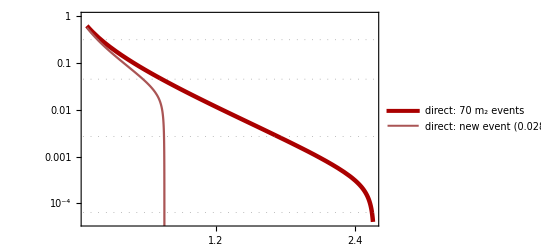

```mathematica
probabiltyNoBHwithMassBelowC[m2_] := Product[SurvivalFunction[𝒟M2ObsFormationClean[event], m2], {event, 1, Length@mXzDataCentralValues2Clean}];
probabiltyNoBHwithMassBelowM[m2_] := Product[SurvivalFunction[𝒟M2ObsFormationMorras[event], m2], {event, 1, Length@mXzDataCentralValues2Morras}];

tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -20, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -20, 0, 1}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -4, 0, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksSmallH = Table[{n, "", tickSmall}, {n, 0.0, 5, 0.05}];
frameTicksLargeH = Table[{n, NumberForm[n, {2,1}], tickLarge}, {n, 0.0, 5, 0.2}];
frameTicksH = Flatten[Join[{frameTicksSmallH, frameTicksLargeH}],1];

plotProbabilityNullC = LogPlot[probabiltyNoBHwithMassBelowC[m2],
  {m2, 0.08, 2.56},
  PlotRange->{All, {4 10^-5, 1}},
  PlotStyle->{{Thickness[0.008], Darker@Red}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, {probSigma[#], ToString@# <> "σ"} & /@ Range[10]}, {frameTicksH, Automatic}},
  GridLines->{None, probSigma[#]& /@ Range[10]},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {
      Style["direct: 70 m_2 events", FontFamily->"Times", FontSize -> 13]
    },
    {0.53,0.85}
  ]
];

plotProbabilityNullM = LogPlot[probabiltyNoBHwithMassBelowM[m2],
  {m2, 0.08, 0.755},
  PlotRange->All,
  PlotStyle->{{Thickness[0.004], Darker@Pink}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, {probSigma[#], ToString@# <> "σ"} & /@ Range[10]}, {frameTicksH, Automatic}},
  GridLines->{None, probSigma[#]& /@ Range[10]},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {
      Style["direct: new event (0.028, 0.76 StyleBox[SubscriptBox[\"M\", \"☉\"],FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]", FontFamily->"Times", FontSize -> 13]
    },
    {0.65,0.75}
  ]
];

plotNewLowMassEvent = Show[plotProbabilityNullC, plotProbabilityNullM]

(*exportOut["plotNewLowMassEvent.pdf", plotNewLowMassEvent]*)
```

```mathematica
sigmaProb@probabiltyNoBHwithMassBelowM[0.57]
```

2.0092

```mathematica
sigmaProb@probabiltyNoBHwithMassBelowC[0.73]
```

2.00203

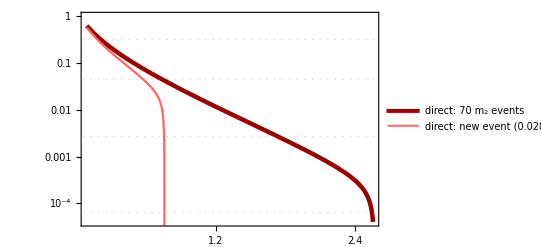

pathOut/plotNewLowMassEvent.pdf

```mathematica
color1i = RGBColor[0, 76/255, 153/255];
color1ii = RGBColor[51/255, 153/255, 255/255];
color1iii = RGBColor[153/255, 0, 0];
color1iv = RGBColor[255/255, 102/255, 102/255];

plotNewLowMassEvent = -Graphics- /. {Darker@Red -> color1iii, Darker@Pink -> color1iv}
exportOut["plotNewLowMassEvent.pdf", plotNewLowMassEvent]
```